```mathematica
(*Data=Import["E:\\Downloads\\RRAM-Relaxation-Master-Model-main\\techA_35hr_truncated.tsv"];*)
Data=Import["E:\\Downloads\\RRAM-Relaxation-Master-Model-main\\techA_35hr_modified.tsv"];
```

```mathematica
(*gt[Addr_,t_]:=
Module[{x},
x=Select[Data,#[[1]]==Addr&];
x[[First@Ordering[Abs[x[[All,2]]-t],1],4]]
]
Addr=DeleteDuplicates[Data[[All,1]]]
t={0,0.01,0.1,1,10,100000};*)

(* After preprocess, everything could be accessed directly through index instead of Select method *)
Addr=DeleteDuplicates[Data[[All,1]]];
Length[Addr]
t={0,0.01,0.1,1,10,100000};
gt[AddrCnt_,tCnt_]:=Data[[(AddrCnt-1)*Length[t]+tCnt,3]]
```

16292

```mathematica
(* Get range number, notice some initial conductance states exceed gmax *)
gmax=40*^-6;
range=Min[#,31]&/@Quotient[gt[#,1]&/@Range[Length[Addr]],(gmax/32)];
AddrList[n_]:=Flatten[Position[range,n]]
rangesPlot={0,8,16,24,31};
AddrPlot=AddrList[#]&/@rangesPlot;
```

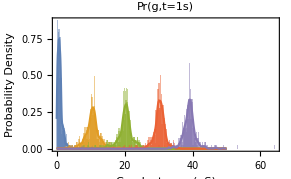

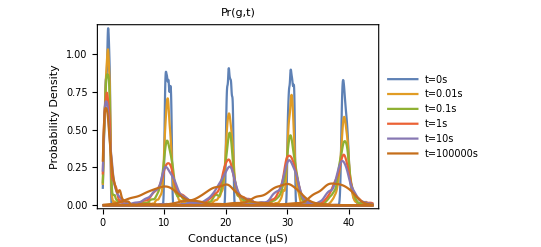

```mathematica
(* Plot conductance distributions at different times, each of the variables have Length[t] elements representing distributions of each time *)
gts=Table[gt[#,tCnt]&/@AddrPlot,{tCnt,Length[t]}];
gtdistKDEs=Table[Table[TruncatedDistribution[{0,∞},SmoothKernelDistribution[gt,MaxMixtureKernels->All]],{gt,gts[[tCnt]]}],{tCnt,Length[t]}];
gtdistKDEpdfs=Table[Table[PDF[gtdistKDE,g],{gtdistKDE,gtdistKDEs[[tCnt]]}],{tCnt,Length[t]}];
scaled=gtdistKDEpdfs/10^6/.{g->x/10^6};
(* Plot PDF with histogram at t=1s *)
Show[Histogram[gts[[4]]*10^6,{0.1},"PDF",ChartStyle->ColorData[97,"ColorList"]],Plot[Evaluate@scaled[[4]],{x,0,gmax*10^6*1.25},PlotRange->All],PlotLabel->"Pr(g,t=1s)",Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
(* Plot as Fig. 13 *)
Show[Table[Plot[scaled[[tCnt]],{x,0,gmax*10^6*1.1},PlotRange->All,PlotStyle->ColorData[97,tCnt],PlotLegends->LineLegend[{"t="<>ToString[t[[tCnt]]]<>"s"}]],{tCnt,Length[t]}],PlotLabel->"Pr(g,t)",Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",None},{"Conductance (μS)",None}}]
```